# Exploring Food Data

Corwin Kerr

## What data is available?

The Wolfram Language has built-in information which powers WolframAlpha. I was curious about exploring the data associated with food, and ended up finding the most cost-effective way to consume calories and making designer-smoothies.

Free form input can be used to start the search for available data.

```mathematica
strawberry=
```

And see what this is behind the scenes:

```mathematica
%//InputForm
```

Entity["Food", 
 {EntityProperty["Food", "FoodType"] -> 
   ContainsExactly[{Entity["FoodType", 
      "Strawberry"]}], 
  EntityProperty["Food", "AddedFoodTypes"] -> 
   ContainsExactly[{}]}]

There is a difference between a Food, FoodType, and FoodTypeGroup. “Food” has the most properties that we can query.

```mathematica
{foodProperties,foodTypeProperties,foodTypeGroupProperties}=EntityProperties[#]&/@{"Food","FoodType","FoodTypeGroup"};
Length/@%
```

{627,32,12}

### The Role of FoodTypeGroup

We can see the 31 FoodTypeGroup which are available.

```mathematica
foodTypeGroup=EntityValue["FoodTypeGroup","Entities"]
```

{alcoholic beverages,berries,breads,candies,carbonated beverages,cheeses,coffee beverages,drinks,fats,fishes,frozen novelties,fruits,greens,juices,meats,milks,nuts,oils,pastas,plants,poultry,preserves,roes,sandwiches,sauces,seafood,seeds,soups,soy,spices,squashes}

Some contain more elements than others...

```mathematica
Length/@EntityValue[foodTypeGroup,"Foods"]
```

EntityValue::nodat: Unable to download data. Some or all results may be missing.

{646,86,1232,1825,415,633,1,2802,347,1093,613,6131,209,1190,1,1872,1185,1319,1377,2676,2553,149,39,283,1009,1,5137,1050,72,3,288}

Say we are interested in making a smoothie, and we need to understand the densities of fruits we pick.

```mathematica
foodTypesOfInterest={Entity["FoodTypeGroup","Fruits"],Entity["FoodTypeGroup","Greens"],Entity["FoodTypeGroup","Juices"]};
```

We can define a function to get densities of food types. The code selects values that are not missing and uses Union to remove duplicate elements.

```mathematica
densityOfFoodType[type_]:=Union[Select[EntityValue[EntityValue[type["Foods"]],"Density"],!MatchQ[#,_Missing]&]]
SetAttributes[densityOfFoodType,Listable]
```

```mathematica
den=densityOfFoodType[foodTypesOfInterest]
```

{{0.0591745 g/cm^3,0.163434 g/cm^3,0.16907 g/cm^3,0.228245 g/cm^3,0.232471 g/cm^3,0.31 g/cm^3,0.346594 g/cm^3,0.405768 g/cm^3,0.418449 g/cm^3,0.422675 g/cm^3,0.464943 g/cm^3,0.473396 g/cm^3,0.490303 g/cm^3,0.502984 g/cm^3,0.50721 g/cm^3,0.512334 g/cm^3,0.574838 g/cm^3,0.591745 g/cm^3,0.604426 g/cm^3,0.608652 g/cm^3,0.621333 g/cm^3,0.625559 g/cm^3,0.629786 g/cm^3,0.634013 g/cm^3,0.63824 g/cm^3,0.65092 g/cm^3,0.659373 g/cm^3,0.680507 g/cm^3,0.697414 g/cm^3,0.718548 g/cm^3,0.731228 g/cm^3,0.735455 g/cm^3,0.748135 g/cm^3,0.754475 g/cm^3,0.760816 g/cm^3,0.78 g/cm^3,0.803083 g/cm^3,0.824217 g/cm^3,0.845351 g/cm^3,0.86 g/cm^3,0.904525 g/cm^3,0.921432 g/cm^3,0.951019 g/cm^3,0.972153 g/cm^3,0.980607 g/cm^3,0.997514 g/cm^3,1.01442 g/cm^3,1.02569 g/cm^3,1.0271 g/cm^3,1.03133 g/cm^3,1.03286 g/cm^3,1.03555 g/cm^3,1.03978 g/cm^3,1.04147 g/cm^3,1.04823 g/cm^3,1.05246 g/cm^3,1.055 g/cm^3,1.05669 g/cm^3,1.06091 g/cm^3,1.06514 g/cm^3,1.06937 g/cm^3,1.0719 g/cm^3,1.0736 g/cm^3,1.07782 g/cm^3,1.08205 g/cm^3,1.0905 g/cm^3,1.09473 g/cm^3,1.09896 g/cm^3,1.10318 g/cm^3,1.12009 g/cm^3,1.12432 g/cm^3,1.14122 g/cm^3,1.1539 g/cm^3,1.19194 g/cm^3,1.28916 g/cm^3,1.34833 g/cm^3,1.35256 g/cm^3,1.4371 g/cm^3,1.67661 g/cm^3,17.5833 g/cm^3},{0.12173 g/cm^3,0.122576 g/cm^3,0.152163 g/cm^3,0.160617 g/cm^3,0.164843 g/cm^3,0.232471 g/cm^3,0.236698 g/cm^3,0.300099 g/cm^3,0.443809 g/cm^3,0.608652 g/cm^3,0.614288 g/cm^3,0.760816 g/cm^3,0.98906 g/cm^3},{0.946392 g/cm^3,0.997514 g/cm^3,1.00174 g/cm^3,1.01442 g/cm^3,1.02118 g/cm^3,1.02287 g/cm^3,1.02569 g/cm^3,1.0271 g/cm^3,1.02795 g/cm^3,1.03133 g/cm^3,1.03286 g/cm^3,1.03555 g/cm^3,1.03978 g/cm^3,1.04147 g/cm^3,1.04401 g/cm^3,1.04485 g/cm^3,1.04823 g/cm^3,1.05 g/cm^3,1.05162 g/cm^3,1.05246 g/cm^3,1.055 g/cm^3,1.05669 g/cm^3,1.05838 g/cm^3,1.06 g/cm^3,1.06176 g/cm^3,1.06514 g/cm^3,1.06852 g/cm^3,1.06937 g/cm^3,1.0719 g/cm^3,1.0736 g/cm^3,1.07782 g/cm^3,1.08205 g/cm^3,1.09473 g/cm^3,1.09896 g/cm^3,1.11586 g/cm^3,1.12432 g/cm^3,1.14122 g/cm^3,1.16658 g/cm^3,1.18913 g/cm^3,1.19194 g/cm^3,1.2 g/cm^3,1.2173 g/cm^3,1.22576 g/cm^3}}

According to WL data, all berries have the same density, but we can visualize the density of fruits. What fruit has a density over 17 g/cm^3?

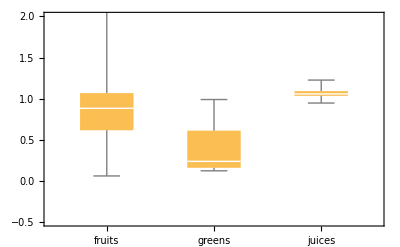

```mathematica
BoxWhiskerChart[den,PlotRange->{-.5,2},ChartLabels->{"fruits","greens","juices"}]
```

It looks like greens tend to be much less dense.

## Fruit Color Space

I decided to investigate the colors of smoothies one could make from different kinds of ingredients.

```mathematica
insideColorsetOfFoodType[type_]:=EntityValue[type,"TypicalInsideColors"]
SetAttributes[insideColorsetOfFoodType,Listable]
```

```mathematica
outsideColorsetOfFoodType[type_]:=EntityValue[type,"TypicalOutsideColors"]
SetAttributes[outsideColorsetOfFoodType,Listable]
```

```mathematica
rgbFromColorset[set_]:=EntityValue[set,EntityProperty["ColorSet","TypicalColorValue"]]
```

Apples have certain exterior colors given as names.

```mathematica
outsideColorsetOfFoodType[]
```

{brown,cream,green,red,white,yellow}

To get instances of these colors:

```mathematica
rgbFromColorset@%
```

{RGBColor[0.6, 0.4, 0.2],RGBColor[1., 0.992157, 0.815686],RGBColor[0, 1, 0],RGBColor[1, 0, 0],RGBColor[1, 1, 1],RGBColor[1, 1, 0]}

Generate a 3D span of these colors.

```mathematica
hull=ConvexHullMesh[List@@@ColorConvert[rgbFromColorset[outsideColorsetOfFoodType[]],"XYZ"]];
```

```mathematica
fruitColorList[fruit_]:=List@@@ColorConvert[rgbFromColorset[outsideColorsetOfFoodType[fruit]],"XYZ"]

fruitColorHull[fruit_]:=ConvexHullMesh[fruitColorList[fruit]]
```

Generate instances of apple colors based on this space.

```mathematica
XYZColor@@@RandomPoint[hull,100]
ChromaticityPlot3D@%
```

{XYZColor[0.5454100122988507, 0.4727558974660292, 0.09637967612317178],XYZColor[0.6916497911952818, 0.7445652403195225, 0.13976727810983525],XYZColor[0.7671777672760153, 0.833345258010569, 0.17679440561091386],XYZColor[0.8293523587001576, 0.8945373225106298, 0.3251193106685676],XYZColor[0.6935370934027981, 0.7069690515809745, 0.2561085857040303],XYZColor[0.611819600220629, 0.5030454306105684, 0.2180724873442651],XYZColor[0.36812423387946513, 0.3963139689438301, 0.13063481537793875],XYZColor[0.38515904959805725, 0.35702638224501426, 0.195509591437383],XYZColor[0.5163573563581482, 0.4047611153628633, 0.14057528434958733],XYZColor[0.6883876370635093, 0.7989962409769736, 0.11053749619645803],XYZColor[0.6501597379624272, 0.8012757906788089, 0.3979177318714203],XYZColor[0.55549630664907, 0.6294780228388298, 0.2752703878602315],XYZColor[0.7203217258823219, 0.8752069882303054, 0.3123391958602514],XYZColor[0.40175765307286126, 0.4782963838041675, 0.13881663792642296],XYZColor[0.46483107727325035, 0.663839120156798, 0.158691198523792],XYZColor[0.7044492884033436, 0.6832374039426793, 0.3323835354229684],XYZColor[0.3350988621462373, 0.43058241646814277, 0.11160671459410199],XYZColor[0.7977594318369888, 0.9020399074792721, 0.4762073680413347],XYZColor[0.49396573560929424, 0.5802089964107519, 0.2916523828048182],XYZColor[0.5962323283512522, 0.6827782030130917, 0.1705820265160245],XYZColor[0.4535021297532752, 0.6488878722429429, 0.21430958530398148],XYZColor[0.8518012601067814, 0.8705356732631978, 0.5794625520856841],XYZColor[0.5298664840606547, 0.4450513755123352, 0.22040843993567572],XYZColor[0.7450884297521186, 0.8600658863752934, 0.4715819315369377],XYZColor[0.4772965588272752, 0.5311166739483374, 0.07659519734680242],XYZColor[0.6245144787526201, 0.6421785484435759, 0.13739074612715807],XYZColor[0.5694986365019671, 0.7411777099902793, 0.23269872312826856],XYZColor[0.8012268677241076, 0.8593663289673258, 0.30175768959706806],XYZColor[0.5313072375160531, 0.5899554443913709, 0.1295692326992567],XYZColor[0.5942361629481033, 0.6224397070426465, 0.27823240273452743],XYZColor[0.6346982161824412, 0.7925856048981311, 0.20560353231709716],XYZColor[0.45788980273766355, 0.3980988602461669, 0.22957575703428124],XYZColor[0.5365262822640419, 0.6715843965136133, 0.19460459424619558],XYZColor[0.4368721031242232, 0.5924798017516312, 0.08275423462873754],XYZColor[0.4154825168825349, 0.3195440309169614, 0.056745327796491996],XYZColor[0.6902103438989727, 0.6879448687417863, 0.22246898186246444],XYZColor[0.6422293560300499, 0.6746216874100658, 0.23778308073503152],XYZColor[0.47924537413987134, 0.4649113411026077, 0.12133270161498577],XYZColor[0.4530646198063023, 0.5622401655186707, 0.24779749181399524],XYZColor[0.6628638782342194, 0.7535733917886341, 0.17693225788429578],XYZColor[0.5642217271955109, 0.5474169017944434, 0.352016969730819],XYZColor[0.5582374767316022, 0.49908365814192546, 0.059217673194707166],XYZColor[0.6368428261476918, 0.6028755542940373, 0.27575384251505686],XYZColor[0.7722614492898311, 0.8186021648337723, 0.2254533666531381],XYZColor[0.6882609847666729, 0.7564013594099307, 0.14351080224294688],XYZColor[0.5901178077429471, 0.695194690738664, 0.10445175660709205],XYZColor[0.44657449346512357, 0.4923896194758367, 0.16824470553663584],XYZColor[0.6705015429667919, 0.6301886944333847, 0.2574837803625726],XYZColor[0.537160710626651, 0.47359844373121696, 0.22077664453054557],XYZColor[0.5411324231400018, 0.6546214678403249, 0.24658945938469878],XYZColor[0.4142041056597432, 0.566264668495636, 0.13472972467066047],XYZColor[0.5639019668238506, 0.6890286721717535, 0.329135440251091],XYZColor[0.7900922403733773, 0.9164288416601615, 0.17857044731638094],XYZColor[0.560677324178016, 0.5471730945443766, 0.36416073846553865],XYZColor[0.7021665981748574, 0.8505214098664396, 0.18563980846633532],XYZColor[0.5185590195307092, 0.5174735906277962, 0.27540237976059345],XYZColor[0.6333188510794977, 0.7442892771419082, 0.1328813151858631],XYZColor[0.4218133447990349, 0.4994426361991021, 0.11364468757311408],XYZColor[0.4477562582700204, 0.6156986189602697, 0.1755298337066704],XYZColor[0.7632487695941487, 0.8205488042207155, 0.20834567105717816],XYZColor[0.5002203751410691, 0.710868142251129, 0.21653070429725962],XYZColor[0.45309715377732507, 0.46060778224722354, 0.27485320316681905],XYZColor[0.36676127336319164, 0.3914248165385871, 0.1132200393637186],XYZColor[0.5481856091037979, 0.7987020225439251, 0.10361570108847351],XYZColor[0.7715842987519353, 0.8827745712825062, 0.3309910106220263],XYZColor[0.48987023177905165, 0.5954705330691207, 0.2659770476260369],XYZColor[0.6346256351921556, 0.7377088015740493, 0.11996024137301242],XYZColor[0.4666752916206013, 0.3988803207048054, 0.1792605366588681],XYZColor[0.5036653008900375, 0.4819556386435463, 0.3267096675217641],XYZColor[0.5116822790694336, 0.39936750549461764, 0.21402031687434697],XYZColor[0.4225746533914917, 0.5702704243893107, 0.10854525240168056],XYZColor[0.5426157455840018, 0.6516574025108138, 0.1786508543234504],XYZColor[0.5278948285685529, 0.7725163196406574, 0.09904791149131331],XYZColor[0.41062694785650955, 0.6763257749037549, 0.1187437262219957],XYZColor[0.5151638565067328, 0.7778219878292759, 0.15148197628979954],XYZColor[0.621797485269359, 0.6280007842201917, 0.07213634209701603],XYZColor[0.7412297444186017, 0.8319778809683406, 0.1500710005278828],XYZColor[0.3568218624692221, 0.3325275779643735, 0.10774577878842151],XYZColor[0.6355011820976274, 0.61415806815962, 0.26878027600228716],XYZColor[0.3939486628819161, 0.4000890360312791, 0.132957091720738],XYZColor[0.5448616651155828, 0.5910330309095401, 0.13117097587318738],XYZColor[0.6033930085690805, 0.5393405353463018, 0.16524484892902414],XYZColor[0.4876225016304808, 0.45029381728975093, 0.22397395226420336],XYZColor[0.6851900144231556, 0.7623694520867809, 0.21448273825884112],XYZColor[0.40507474008467537, 0.28961309589395023, 0.03352236647784401],XYZColor[0.5477679454697796, 0.6591607639294751, 0.26042383654769685],XYZColor[0.7732751997916535, 0.797427049980976, 0.49134556648821703],XYZColor[0.5717381073105198, 0.7071703743007246, 0.10812086999069515],XYZColor[0.8115280596301769, 0.8702862695540509, 0.4309219518832844],XYZColor[0.5762188424608731, 0.5561311030297663, 0.3702232041405985],XYZColor[0.7155640352005678, 0.8193628207535245, 0.1448166613009897],XYZColor[0.6273887293646309, 0.6095743770799168, 0.37981619353338447],XYZColor[0.5215882654423561, 0.6064446503393627, 0.24565464215773447],XYZColor[0.8188911721590447, 0.8389239397515021, 0.5520677710372875],XYZColor[0.5653547242755795, 0.6853696126522476, 0.10092331564419765],XYZColor[0.5470591510156465, 0.5101909584405698, 0.18094537679001665],XYZColor[0.4572855859247257, 0.6704973319406503, 0.10429837545262466],XYZColor[0.5709803288967447, 0.7379301116359834, 0.09753505218984793],XYZColor[0.6284761983237698, 0.8124457966024278, 0.36494658061236207],XYZColor[0.8761156840751622, 0.9371839804708691, 0.5317001865125554]}

-Graphics3D-

```mathematica
XYZColor@@@RandomPoint[fruitColorHull[LinguisticAssistant],100]
ChromaticityPlot3D@%
```

{XYZColor[0.5152070401040167, 0.6415300989546749, 0.07816311981975005],XYZColor[0.4217949310986188, 0.5619174711130707, 0.06997231816039204],XYZColor[0.6424980880355278, 0.7716357444612765, 0.09284748471512388],XYZColor[0.4447252384135195, 0.5924787754171641, 0.07377845579750837],XYZColor[0.6877308381159069, 0.7820909040085386, 0.09223540652002336],XYZColor[0.613010303782153, 0.6953689912819456, 0.08192915505967552],XYZColor[0.49695773005386684, 0.42006647056044133, 0.043008898653611946],XYZColor[0.605748408030348, 0.5736383521711813, 0.06246436609510726],XYZColor[0.480539689242022, 0.4521193320857934, 0.04907262241586924],XYZColor[0.595021800697187, 0.5860186682009839, 0.06503097017836462],XYZColor[0.4456003951504579, 0.284180190940967, 0.023494949887597864],XYZColor[0.4461997554630597, 0.6760523663312412, 0.08732167307154688],XYZColor[0.4388633734815205, 0.7168974413608956, 0.09435317268647332],XYZColor[0.5857081172949113, 0.5442574289797876, 0.05870261599915898],XYZColor[0.45967399050592406, 0.4837967929624612, 0.0553028810376719],XYZColor[0.45975355372434157, 0.5849385649815483, 0.07178033371041716],XYZColor[0.44223130929553467, 0.4084297404801368, 0.043914484862892615],XYZColor[0.5395018818782583, 0.6613848629618319, 0.08015471599854124],XYZColor[0.519031670171265, 0.6862922174902725, 0.08526150616464241],XYZColor[0.6611014114646778, 0.7541312827030382, 0.08904261031711555],XYZColor[0.47508666761833573, 0.478303114775808, 0.053618572685323],XYZColor[0.6646108353400002, 0.686511087563034, 0.07784390929740964],XYZColor[0.7317988323194633, 0.8274616042519715, 0.09737261180872592],XYZColor[0.43535247145530526, 0.5134585001026014, 0.06138159186502202],XYZColor[0.47577211336799746, 0.3143958070412984, 0.026874015195966],XYZColor[0.5668100508119291, 0.5427550895822435, 0.05942533306245537],XYZColor[0.6602476288180674, 0.6408621341723825, 0.07062858272357755],XYZColor[0.6540277884379586, 0.6938343121292359, 0.07957908670037593],XYZColor[0.48818555738114633, 0.4421882680869778, 0.04706286102114719],XYZColor[0.5228278278830651, 0.5851283391178139, 0.06858202464209304],XYZColor[0.5669925229953385, 0.7874171256310555, 0.0992848171927038],XYZColor[0.6252879455609682, 0.6521458818146627, 0.07425716433261306],XYZColor[0.5248567665077117, 0.7289266647097593, 0.09191075998282612],XYZColor[0.4731977274423714, 0.5536672908871937, 0.06599622730406324],XYZColor[0.6738341748404254, 0.8425028909155027, 0.1027912949980908],XYZColor[0.445797025800697, 0.5153541262524467, 0.06115575986922162],XYZColor[0.5170212232936859, 0.7568437701144557, 0.0968611420325888],XYZColor[0.5770277504756489, 0.5425780758689467, 0.058873369031678766],XYZColor[0.4510209782820296, 0.27827647667577043, 0.022255392643410626],XYZColor[0.47323372214901144, 0.4997116056082494, 0.05720205250822663],XYZColor[0.6971911606191648, 0.8001579384933073, 0.09469517138514483],XYZColor[0.44214655126038926, 0.5529113326869733, 0.06746277730242779],XYZColor[0.4610130740242362, 0.33770979074303137, 0.03142876140707755],XYZColor[0.5691948821254194, 0.6801371212222083, 0.08169028246082108],XYZColor[0.5387046190010808, 0.6990457604043592, 0.08633255358377225],XYZColor[0.5320563219783119, 0.6929899026874871, 0.08568609814234174],XYZColor[0.576033956562144, 0.8096976502346601, 0.10245263602353823],XYZColor[0.7187044019198756, 0.762932525693741, 0.08752769553570615],XYZColor[0.7744731486653871, 0.8655317588990323, 0.1013915115216843],XYZColor[0.5762298586981907, 0.5833386062064787, 0.06555633853215144],XYZColor[0.6723954300809039, 0.7631931874400362, 0.0899410667341162],XYZColor[0.476760034659834, 0.4153876838776026, 0.04328053624879684],XYZColor[0.6145609483633157, 0.6480846192874811, 0.07414455604053508],XYZColor[0.45591462229366175, 0.2788188427495662, 0.022093232291526883],XYZColor[0.44327368896903796, 0.6463929651892404, 0.08263834131154929],XYZColor[0.5394095428652746, 0.7049103723001985, 0.0872521293856484],XYZColor[0.5162515781949838, 0.5601467664130303, 0.06484784655323536],XYZColor[0.6615803307865109, 0.7686865049704086, 0.09138993266355654],XYZColor[0.4635002336294481, 0.298023378927393, 0.024834338575578478],XYZColor[0.47545404632474675, 0.47984335942090334, 0.05385075396949253],XYZColor[0.40789686134781916, 0.5316350648647333, 0.0657492019332058],XYZColor[0.6192279599616765, 0.6309115518263777, 0.071107185682053],XYZColor[0.48626580221617605, 0.4332668730120343, 0.04570736416828209],XYZColor[0.6531292179841321, 0.6978865098285676, 0.08028541571693183],XYZColor[0.6931897016959929, 0.7358640093660678, 0.08442303806506762],XYZColor[0.719472941114, 0.7649911808303469, 0.08782381589982],XYZColor[0.6628750988453376, 0.6775472664481205, 0.07647207766002767],XYZColor[0.45277520165469076, 0.46284262386563413, 0.05224150039489514],XYZColor[0.414765067103112, 0.6451204152484957, 0.08389053830189672],XYZColor[0.6914745218974383, 0.7235948065563742, 0.08251152653088331],XYZColor[0.5943496886428034, 0.5623859870960527, 0.06121432429160511],XYZColor[0.6160581317714174, 0.7208605815607062, 0.08592708863090093],XYZColor[0.47832518445995653, 0.6273048325992714, 0.07773329803333529],XYZColor[0.45887907191558736, 0.30313562346827555, 0.02590399388395651],XYZColor[0.6590369481020733, 0.8310334440926994, 0.10167987316631333],XYZColor[0.5265087610971969, 0.7500453024213011, 0.095267563350526],XYZColor[0.4631696351605564, 0.7121841429857872, 0.09234070320962773],XYZColor[0.47438487321521206, 0.6587019203035037, 0.08305133409089284],XYZColor[0.6965913949117274, 0.708770253420153, 0.0798338258981172],XYZColor[0.7207369164302029, 0.7774214577919674, 0.08978467568172191],XYZColor[0.41127304007216364, 0.7296606523411174, 0.09784554883945328],XYZColor[0.5899563369059688, 0.6515735333462864, 0.07597278105918014],XYZColor[0.4508958849476068, 0.5566486223826032, 0.06762384376928204],XYZColor[0.455108061731578, 0.6574496780845099, 0.08383419639049873],XYZColor[0.44627972037232977, 0.5106280570528487, 0.060360912060973354],XYZColor[0.43076325130277193, 0.6537437640413217, 0.08447668931104069],XYZColor[0.5178192086594994, 0.5227575403395639, 0.058674838337578986],XYZColor[0.6231248961481115, 0.6523460571050568, 0.07440052616301332],XYZColor[0.6878345724780738, 0.7388112360169521, 0.08517747072203469],XYZColor[0.8135757533902612, 0.9329001302381399, 0.11036755510520802],XYZColor[0.5102610698371658, 0.5996098233551104, 0.07158523471973374],XYZColor[0.5563169166027634, 0.6282301182629717, 0.07389111018195205],XYZColor[0.5475538102007957, 0.43654780593099396, 0.04310422595769042],XYZColor[0.6272739060476538, 0.651745144537973, 0.07409018646394594],XYZColor[0.46341612138253, 0.2987133625960912, 0.024951080971782114],XYZColor[0.6495335769889405, 0.6963342624992973, 0.08021655690915594],XYZColor[0.417521741591721, 0.487176903352981, 0.05801176795834606],XYZColor[0.49877617216173586, 0.6363762607139825, 0.07816449407380337],XYZColor[0.5446211693859406, 0.7410517573888438, 0.09287471628681551],XYZColor[0.43139905451469496, 0.5447010570140819, 0.06667511738164057]}

-Graphics3D-

To visualize the possible colors in a collection of fruits, we combine the color lists.

```mathematica
cols=fruitColorList[Interpreter["Food"][#]]&/@{"Apple","Orange","Carrot","Banana","Blueberry","Blackberry","Strawberry"}
```

{{{0.19481,0.168135,0.0409827},{0.904554,0.964894,0.559783},{0.385065,0.716879,0.0971045},{0.436075,0.222504,0.0139322},{0.96422,1.,0.82521},{0.82114,0.939383,0.111037}},{{0.518495,0.375946,0.0347166}},{{0.,0.,0.},{0.904554,0.964894,0.559783},{0.518495,0.375946,0.0347166},{0.82114,0.939383,0.111037}},{{0.904554,0.964894,0.559783},{0.82114,0.939383,0.111037}},{{0.14308,0.0606169,0.714173},{0.96422,1.,0.82521}},{{0.,0.,0.},{0.436075,0.222504,0.0139322},{0.96422,1.,0.82521}},{{0.436075,0.222504,0.0139322},{0.96422,1.,0.82521}}}

```mathematica
XYZColor@@@RandomPoint[ConvexHullMesh[Flatten[cols,1]],100]
```

{XYZColor[0.3616815992272263, 0.5551114121759017, 0.1650932871589199],XYZColor[0.7341105017001751, 0.7302792847947323, 0.6133952373922859],XYZColor[0.3702030156751762, 0.32547182098969507, 0.40467696846491774],XYZColor[0.36311918509544283, 0.3254253114243998, 0.17377183526831808],XYZColor[0.3035780385477024, 0.3023400646636666, 0.10925887520048172],XYZColor[0.6091169944023606, 0.6799197397090907, 0.5342707471497666],XYZColor[0.4855468676083535, 0.5584888100673356, 0.34352917846015385],XYZColor[0.4086547529197798, 0.39278813099085064, 0.6530578424876462],XYZColor[0.5154211877307194, 0.4910943557226123, 0.46919041691910623],XYZColor[0.6969703086275726, 0.8656838677833042, 0.16972924741506434],XYZColor[0.355281168493777, 0.31773523612099763, 0.6492848966281232],XYZColor[0.19562486639948273, 0.13683665394303002, 0.21710516670739033],XYZColor[0.4117163240594025, 0.5101914493298524, 0.4733813008537612],XYZColor[0.36928461433330273, 0.4739161334270129, 0.3806194336960965],XYZColor[0.3111005866327178, 0.29791235463013976, 0.5075266266698838],XYZColor[0.5116032561696043, 0.6728339537352911, 0.3378381067486048],XYZColor[0.8421749651977534, 0.9096855420306432, 0.36221852159843826],XYZColor[0.3688487268047992, 0.588836097601913, 0.2747309319137249],XYZColor[0.3968688139072015, 0.32864382614672516, 0.23892669600355643],XYZColor[0.28807795199354114, 0.3490287526625423, 0.047507344269181684],XYZColor[0.25802046764448006, 0.24723103993332074, 0.18001212289783053],XYZColor[0.6406507283686073, 0.7514399968327216, 0.5525985826444754],XYZColor[0.48684334577522115, 0.5885838139396283, 0.13816971671235156],XYZColor[0.6347934970235215, 0.6541021921914242, 0.3171160010611832],XYZColor[0.18634248346721416, 0.19108413386625644, 0.4375305194089557],XYZColor[0.6382736870868367, 0.7052861560396378, 0.10334046618336934],XYZColor[0.7457603307061881, 0.8636406112161746, 0.376937531884043],XYZColor[0.29249171789704265, 0.2093143884773251, 0.23911240225161368],XYZColor[0.5325400068408414, 0.524826299632679, 0.6887969039445839],XYZColor[0.13889196748875154, 0.17836712112190722, 0.2886622375819553],XYZColor[0.3770741249090751, 0.28404759943166125, 0.27711219328288583],XYZColor[0.7327428178470207, 0.7115787296438075, 0.43340238094275485],XYZColor[0.17760028361889202, 0.27884177946573707, 0.16948448806276306],XYZColor[0.3280151648997781, 0.4429407446008219, 0.14356233947983155],XYZColor[0.4131871957314318, 0.5784840507447572, 0.1068840157159725],XYZColor[0.2405220929042261, 0.18497795189618305, 0.6613358553418179],XYZColor[0.6041196221926955, 0.8187712188536097, 0.3138755903783331],XYZColor[0.5433520888488931, 0.45024214297027354, 0.4413297781737652],XYZColor[0.18838276569420798, 0.12821797142599245, 0.5509444493169237],XYZColor[0.5106792444300697, 0.4825339566303578, 0.3237633055114396],XYZColor[0.334206867280166, 0.3129761156702461, 0.04884038863475337],XYZColor[0.5239302417504975, 0.5795577494379541, 0.17470643868482238],XYZColor[0.5262247072426166, 0.5783310966081011, 0.4146768057087292],XYZColor[0.6981685380453951, 0.783118210099223, 0.29231171016053337],XYZColor[0.5597632437403582, 0.5151817142068086, 0.5760828440584084],XYZColor[0.2579496779006648, 0.3345485538638254, 0.14394472044894657],XYZColor[0.26415916482939183, 0.2899886218018003, 0.09957812273311595],XYZColor[0.598952731321006, 0.6176742199274688, 0.18044448965413584],XYZColor[0.39526455546840855, 0.3498951881531488, 0.6940848974695565],XYZColor[0.4780869039716563, 0.56357547639055, 0.26046442806241166],XYZColor[0.5821041437294193, 0.8112546467901122, 0.10410512130072547],XYZColor[0.773451097705557, 0.8473229602075437, 0.21673930740107406],XYZColor[0.6643765127796409, 0.6022552195398013, 0.49841583405820156],XYZColor[0.6554052751011087, 0.8177338853737935, 0.44038635481308164],XYZColor[0.5876656263488161, 0.5464377166843467, 0.603104439884354],XYZColor[0.3695308055003411, 0.4567528014532459, 0.45496349907692435],XYZColor[0.5308819299687665, 0.42074340411264066, 0.06719400195367087],XYZColor[0.3376342717689841, 0.24311776460935752, 0.11124537218641883],XYZColor[0.5339105384128907, 0.7473407320857911, 0.31697136346034294],XYZColor[0.48503104725747004, 0.3774514322293362, 0.05757854054089917],XYZColor[0.7838212250847291, 0.8115227855842942, 0.34808773124031667],XYZColor[0.7433365687489374, 0.7737547850188077, 0.7308344072776592],XYZColor[0.710741281576111, 0.8320415400236533, 0.10001253193564552],XYZColor[0.3422149418084107, 0.3646432392297422, 0.22320099248888814],XYZColor[0.31104323857460325, 0.46642649677210113, 0.3321436807676562],XYZColor[0.19404419881573942, 0.1817624310439344, 0.2802778421074902],XYZColor[0.5619002964128307, 0.7964345112807857, 0.18345040009225044],XYZColor[0.5112610345102871, 0.7299644952820671, 0.2707594578179743],XYZColor[0.19158010080455046, 0.13193491401058444, 0.2257298933652202],XYZColor[0.6825460346171611, 0.6459413611033448, 0.21399301342501353],XYZColor[0.44005441336932594, 0.5186387836808953, 0.417098874832705],XYZColor[0.44732962761629624, 0.5525748801246188, 0.2831335851738169],XYZColor[0.5720373112797951, 0.6797320071474343, 0.4359690422386234],XYZColor[0.21490831707328872, 0.12609120739659152, 0.18138636974433398],XYZColor[0.6587162203918367, 0.6484487539064304, 0.6949552179979485],XYZColor[0.34464011107565773, 0.22420920458296079, 0.10735826503994272],XYZColor[0.439885595792615, 0.5316944238219284, 0.2000180846102494],XYZColor[0.41194028081097656, 0.3703204881627741, 0.6134195543782518],XYZColor[0.10686659926636077, 0.09072956229877971, 0.11947014956426005],XYZColor[0.5234781711533495, 0.5379920940168349, 0.49529875473782015],XYZColor[0.7594451818209308, 0.8888087516535524, 0.10925863475667585],XYZColor[0.5061537936725734, 0.3629867285363929, 0.19481366703504388],XYZColor[0.6733051991506526, 0.6718299393453452, 0.6334981301009558],XYZColor[0.5115640182778128, 0.5603675528201894, 0.4563616903178159],XYZColor[0.2844842880939763, 0.26368557978221696, 0.18751356589736934],XYZColor[0.6226019124502918, 0.6796275687107068, 0.3603433598704485],XYZColor[0.4604404920728299, 0.4765900399772621, 0.07263144405217958],XYZColor[0.3086381423318477, 0.31433683897442843, 0.06034177907958804],XYZColor[0.5590349369783659, 0.7569578931592239, 0.3166423954523291],XYZColor[0.41386346741278135, 0.3396489225083784, 0.535235353708242],XYZColor[0.5848598195415559, 0.5140039947180769, 0.39767963157053365],XYZColor[0.7962026791209197, 0.7987379621015501, 0.6160737542589819],XYZColor[0.33007708341838227, 0.4318917024873067, 0.10992079991078973],XYZColor[0.39631514225708686, 0.38802575927324645, 0.21209831815214486],XYZColor[0.5345225893277633, 0.4785843646518121, 0.40733333915284187],XYZColor[0.1204348008995123, 0.21752769955991835, 0.03309058471258142],XYZColor[0.3444792845147412, 0.17393914873556382, 0.1842967535479666],XYZColor[0.6937843492370731, 0.8652313130943018, 0.38163611581789614],XYZColor[0.7047549146341073, 0.8226451138110923, 0.261592363433904],XYZColor[0.571249867346273, 0.5568322221327665, 0.6887279433136096]}

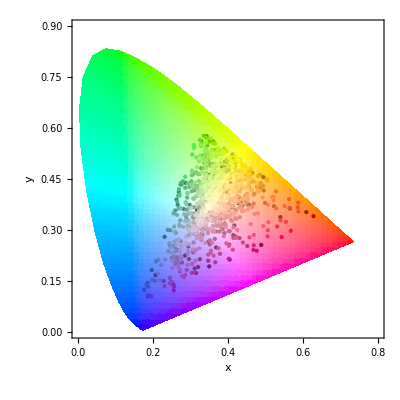

```mathematica
ChromaticityPlot[XYZColor@@@RandomPoint[ConvexHullMesh[Flatten[cols,1]],1000]]
```

```mathematica
fruitColorList[Interpreter["Food"]["Orange"]]
```

{{0.518495,0.375946,0.0347166}}

Let’s fill some fruitbowls with these fruits.

#### Salad bowl

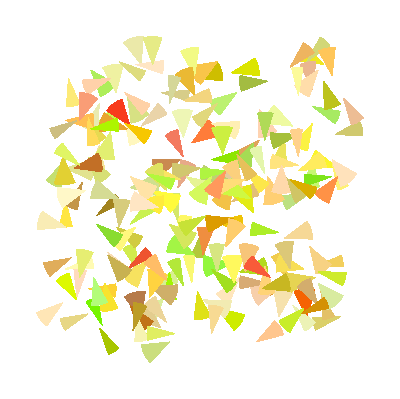

```mathematica
appleImage=Graphics[Table[{XYZColor@RandomPoint[hull],Disk[RandomInteger[{0,100},2]/10,1,{#[[1]],#[[1]]+#[[2]]}&@{RandomReal[{0,2Pi}],RandomReal[{Pi/8,Pi/4}]}]},200]]
```

```mathematica
rgbFromColorset@outsideColorsetOfFoodType[]
```

{RGBColor[0, 0, 0],RGBColor[1., 0.992157, 0.815686],RGBColor[1, 0.5, 0],RGBColor[1, 1, 0]}

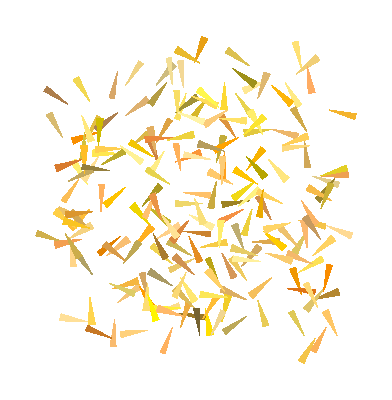

```mathematica
carrotImage=Graphics[Table[{XYZColor@RandomPoint[fruitColorHull[]],Disk[RandomInteger[{0,100},2]/10,1,{#[[1]],#[[1]]+#[[2]]}&@{RandomReal[{0,2Pi}],RandomReal[{Pi/16,Pi/12}]}]},200]]
```

```mathematica
hullIn=ConvexHullMesh[List@@@ColorConvert[rgbFromColorset[insideColorsetOfFoodType[LinguisticAssistant]],"XYZ"]];
```

#### Move each fruit color in color space from fresh to brown